# Relativitic Collision

```mathematica
(* Main Formula *)
EE=T+m c^2; (* T,m *)
EE^2=(p c)^2+(m c^2)^2; (* p, m *)
p=v/c^2 EE; (* p, v *)
(* there are { EE, T, m , p } as main unknown, extra is v *)

(* p= {m, v} *)
p= (m v)/(√(1-(v/c)^2)) ;
p=√(2  m T+T^2/c^2);
```

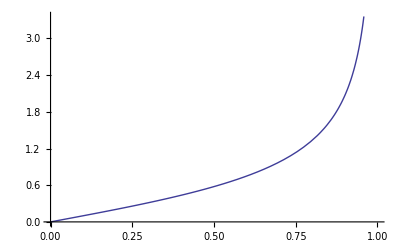

```mathematica
Plot[(m v)/(√(1-(v/c)^2)) /.{m->1,v->β,c->1},{β,0,1}]
```

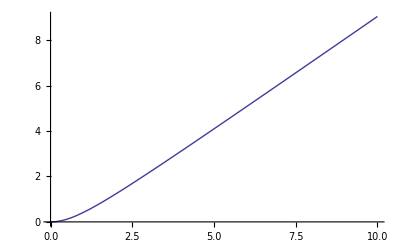

```mathematica
(* T = {m,p} *)
T=-c^2 m±√(c^4 m^2+c^2 p^2);
Plot[-c^2 m+√(c^4 m^2+c^2 p^2)/.{c->1,m->1},{p,0,10}]
```

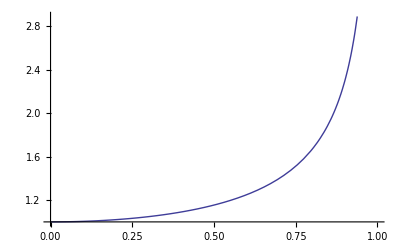

```mathematica
(* EE= {m, v} *)
EE=(m c^2)/(√(1-(v/c)^2));
Plot[(m c^2)/(√(1-(v/c)^2))/.{m->1,v-> β c}/.c->1,{β,0,1}]
```

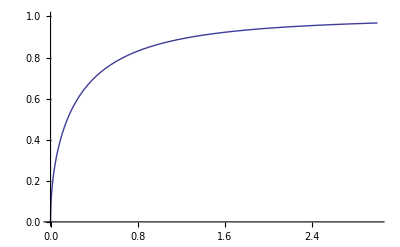

```mathematica
(* v = { m, T } *)
v=(c √(T (2 c^2 m+T)))/(c^2 m+T);
Plot[(c √(T (2 c^2 m+T)))/(c^2 m+T)/.{m->1,c->1},{T,0,3},PlotRange->{0,1}]
```

## 2 same Mass Collision (2 - D) (CM frame)

```mathematica
(* Initial condition *)
E1=T+m c^2;
E2=m c^2;
E1^2== (p1 c)^2+(m c^2)^2;
```

```mathematica
(* Becomes One *)
(* Since mass are the same, The K.E. will be splited equally, in the center mass frame *)
E1a=T/2+m c^2;
E2a = T/2+m c^2;
p1=√(2  m T+T^2/c^2);
p1a=√(2  m T+T^2/c^2)/.{T->T/2}
Solve[p1/2==p1a Cos[θ],θ]
```

√(m T+T^2/(4 c^2))

{{θ→-ArcCos[(c^2 √((T (2 c^2 m+T))/c^2) √((T (4 c^2 m+T))/c^2))/(T (4 c^2 m+T))]},{θ→ArcCos[(c^2 √((T (2 c^2 m+T))/c^2) √((T (4 c^2 m+T))/c^2))/(T (4 c^2 m+T))]}}

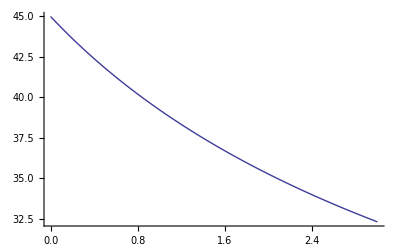

```mathematica
Plot[ArcCos[(c^2 √((T (2 c^2 m+T))/c^2) √((T (4 c^2 m+T))/c^2))/(T (4 c^2 m+T))]*180/π/.{m->1,c->1},{T,0,3},PlotRange->{0,All}]
```